# QED calculation: Peskin Sec. 5

## e^-μ^-→e^-μ^- (QED): Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
SetDirectory[FileNameJoin[{$HomeDirectory,"Documents","Dropbox","FeynLecture"}]];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 4 Jan 12

FormCalc 7.3

by Thomas Hahn

last revised 12 Jan 12

### Create Topology

```mathematica
topologies=CreateTopologies[0,2->2];
(*Paint[topologies];*)
```

### Insert Particles

Manual P.74 has a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes}];
```

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SM.mod

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 114 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 4 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

> Top. 1: 4 diagrams

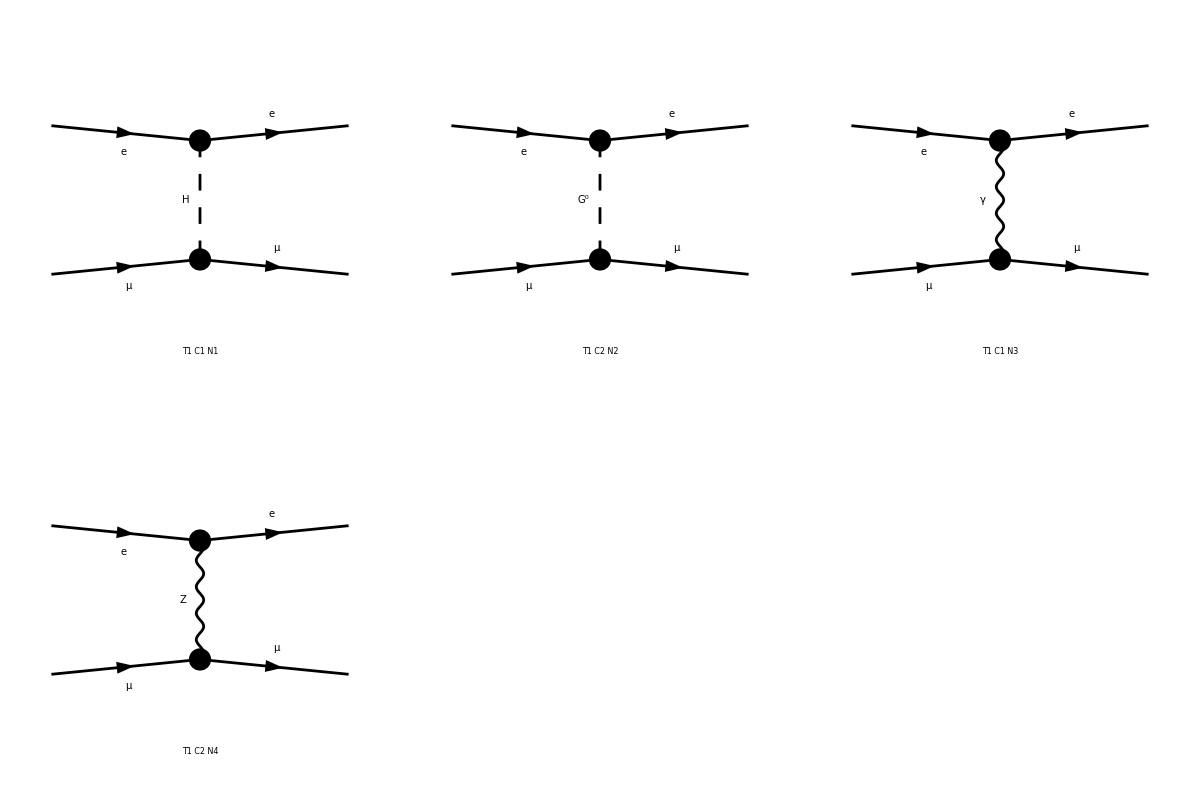

```mathematica
Paint[diagrams];
```

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

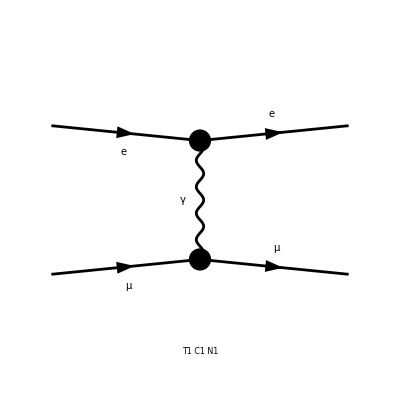

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
amplitude//.Abbr[]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

Amp[{ME,MM}→{ME,MM}][4 Alfa π Den[T,0] Mat[F1]+2 Alfa π Den[T,0] Mat[F2]-4 Alfa π Den[T,0] Mat[F3]-2 Alfa π Den[T,0] Mat[F4]]

Amp[{ME,MM}→{ME,MM}][4 Alfa π Den[T,0] Mat[(<v1|1|u2>) (<u3|1|v4>)]-4 Alfa π Den[T,0] Mat[(<v1|5|u2>) (<u3|5|v4>)]+2 Alfa π Den[T,0] Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]-2 Alfa π Den[T,0] Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]]

HelicityME returns AVERAGE!

```mathematica
SquaredHelicityME=SquaredME[amplitude]//.HelicityME[amplitude];
MatrixElement=2^2*(SquaredHelicityME//.{Hel[_]->0})
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

4 (4 Alfa2 π^2 (ME2^2-2 ME2 (2 ME MM-3 MM2+S)-(MM2-S) (4 ME MM-MM2+S)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2+(MM2-S) (4 ME MM+MM2-S)-ME2 (-4 ME MM-6 MM2+2 S)) Den[T,0]^2-4 Alfa2 π^2 (-ME2^2-MM2^2+2 MM2 S+2 ME2 (MM2+S)-S (S+2 T)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2/2+2 ME MM MM2+MM2^2/2-2 ME MM S-MM2 S+S^2/2-2 MM2 T+S T+T^2-ME2 (-2 ME MM-7 MM2+S+2 T)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2/2-2 ME MM MM2+MM2^2/2+2 ME MM S-MM2 S+S^2/2-2 MM2 T+S T+T^2-ME2 (2 ME MM-7 MM2+S+2 T)) Den[T,0]^2+8 Alfa2 π^2 (MM2 T+ME2 (-4 MM2+T)-2 ME MM (ME2+MM2-U)) Den[T,0]^2+8 Alfa2 π^2 (MM2 T+ME2 (-4 MM2+T)+2 ME MM (ME2+MM2-U)) Den[T,0]^2)

Or more simply, (if one ignores helicity configuration...)

```mathematica
_Hel=0;
MatrixElement=2^2*SquaredME[amplitude]//.HelicityME[amplitude]
```

> 16 helicity matrix elements

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

4 (4 Alfa2 π^2 (ME2^2-2 ME2 (2 ME MM-3 MM2+S)-(MM2-S) (4 ME MM-MM2+S)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2+(MM2-S) (4 ME MM+MM2-S)-ME2 (-4 ME MM-6 MM2+2 S)) Den[T,0]^2-4 Alfa2 π^2 (-ME2^2-MM2^2+2 MM2 S+2 ME2 (MM2+S)-S (S+2 T)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2/2+2 ME MM MM2+MM2^2/2-2 ME MM S-MM2 S+S^2/2-2 MM2 T+S T+T^2-ME2 (-2 ME MM-7 MM2+S+2 T)) Den[T,0]^2+4 Alfa2 π^2 (ME2^2/2-2 ME MM MM2+MM2^2/2+2 ME MM S-MM2 S+S^2/2-2 MM2 T+S T+T^2-ME2 (2 ME MM-7 MM2+S+2 T)) Den[T,0]^2+8 Alfa2 π^2 (MM2 T+ME2 (-4 MM2+T)-2 ME MM (ME2+MM2-U)) Den[T,0]^2+8 Alfa2 π^2 (MM2 T+ME2 (-4 MM2+T)+2 ME MM (ME2+MM2-U)) Den[T,0]^2)

```mathematica
MatrixElement//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}//FullSimplify
```

(2 e^4 (2 (MM2-S)^2+2 S T+T^2))/T^2

```mathematica
OurResult=%//.{S->(kk+EE)^2,T->-2 kk^2(1-CosTheta)}
```

(e^4 (4 (1-CosTheta)^2 kk^4-4 (1-CosTheta) kk^2 (EE+kk)^2+2 (-(EE+kk)^2+MM2)^2))/(2 (1-CosTheta)^2 kk^4)

```mathematica
PeskinResult=(2 e^4)/(kk^2(1-CosTheta)^2)((EE+kk)^2+(EE+kk CosTheta)^2-MM2(1-CosTheta))
FullSimplify[OurResult==PeskinResult,Assumptions->EE^2==kk^2+MM2]
```

(2 e^4 ((EE+kk)^2+(EE+CosTheta kk)^2-(1-CosTheta) MM2))/((1-CosTheta)^2 kk^2)

True